T == Tree level
L == Loop level

```mathematica
LH1M=Higgs1Mod/.{phi2->0,phiS->0};
LH2M=Higgs2Mod/.{phi2->0,phiS->0};
LH2P=Higgs2Phase/.{phi2->0,phiS->0};
LSM=SingletMod/.{phi2->0,phiS->0};
LSP=SingletPhase/.{phi2->0,phiS->0};
```

```mathematica
LVac=Flatten[{Solve[LH1M==0,mH1][[1]],
Solve[LH2M==0,mH2][[1]],
Solve[LSM==0,MS][[1]],
phi2->0,
phiS->0}];
```

```mathematica
LN6=(Mneut+Mne1l)//.LVac;
LC3=(Mchar+Mch1l)//.LVac;
```

```mathematica
MslN=MslepN//.LVac//Simplify;
MslC=MslepC//.LVac//Simplify;
```

```mathematica
Mcχ=Mchχ//.LVac//Simplify;
McχCT=MchχCT//.LVac//Simplify;
Mnχ=Mneχ//.LVac//Simplify;
```

```mathematica
prec=50;
$MinPrecision=prec;
TeV=10^12;GeV=10^9;MeV=10^6;
vSq=SetPrecision[(174GeV)^2,prec];
vSqHiggs = (vSq - σν[1]^2- σν[2]^2- σν[3]^2)/.{σn[3]->0,σν[i_]->0};
mW=SetPrecision[80.403GeV,prec];
mZ=SetPrecision[91.1876GeV,prec];
αew=SetPrecision[1/127.908957,prec];θw=SetPrecision[ArcSin[Sqrt[0.23124]],prec];mtPole=SetPrecision[180GeV,prec];
αstrong=SetPrecision[0.102,prec];
mup=SetPrecision[1.5MeV,prec];
mcharm=SetPrecision[1.1GeV,prec];mtop=SetPrecision[mtPole/(1+4*αstrong/(3 Pi)),prec];
mdown=SetPrecision[3MeV,prec];
mstrange=SetPrecision[60MeV,prec];
mbottom=SetPrecision[4.1GeV,prec];
melectron=SetPrecision[0.511MeV,prec];
mmuon=SetPrecision[105.66MeV,prec];
mtau=SetPrecision[1.777GeV,prec];
Ytop=SetPrecision[mtop /v2,prec];
Ybtm=SetPrecision[mbottom /v1,prec];
Ytau=SetPrecision[mtau /v1,prec];
```

```mathematica
g1 := SetPrecision[Sqrt[(2*Tan[θw]^2*mW^2)/vSq], prec];
g2 := SetPrecision[mW*Sqrt[2/vSq], prec];
v1 = Sqrt[vSqHiggs/(1 + Tan[β]^2)];
v2 = v1*Tan[β];
```

```mathematica
2000*0.7
```

1400.

```mathematica
β = SetPrecision[ArcTan[5.0], prec];
Aλ=400GeV;
Aκ=0GeV;
μ=2000*λ*GeV;
{λ,κ}={0.7,0.007};
Mone=300GeV;
Mle=500GeV;
Mqud=1TeV;
Ae=-2.5TeV;
Aud=1TeV;
```

```mathematica
results=Table[0,{i,1,100}];
```

```mathematica
loop over foo bar
```

```mathematica
z=0;
For[j=0,j<10,
j++;
For[k=0,k<10,
k++;
prec=50;
$MinPrecision=prec;
Abtm=SetPrecision[Aud,prec];  (*used with loops only*)
Akappa=SetPrecision[Aκ,prec];
Alambda=SetPrecision[Aλ,prec];
AlambdaN=SetPrecision[-250 GeV,prec];(* No effect? *)
An11=SetPrecision[TeV,prec];(* No effect? *)
An12=SetPrecision[TeV,prec];(* No effect? *)
An13=SetPrecision[TeV,prec];(* No effect? *)
Atau=SetPrecision[Ae,prec];
Atop=SetPrecision[Aud,prec]; (*used with loops only*)
kappa=SetPrecision[κ, prec];
ksi=SetPrecision[0,prec];(* Only neede for CPV *)
lambda=SetPrecision[λ, prec];
lambdaN=SetPrecision[0.01*j, prec];(* No effect? *)
M1=SetPrecision[Mone,prec];
M2=SetPrecision[2*Mone,prec];
MD33=MQ33=MU33=SetPrecision[Mqud,prec];(*used with loops only*)
ME11=ME22=ME33=ML11=ML22=ML33=SetPrecision[Mle,prec];
ME12=ME13=ME23=SetPrecision[0,prec];
ML12=ML13=ML23=SetPrecision[0,prec];
MN33=SetPrecision[k*25GeV,prec];
Rsc=SetPrecision[500GeV,prec]; (*used with loops only*)
vevS=SetPrecision[μ/lambda,prec];(* No effect? *)
Yn11=SetPrecision[10^-5,prec];
Yn12=SetPrecision[10^-5,prec];
Yn13=SetPrecision[10^-5,prec];
{valNsc,vecNsc}=Eigensystem[LN6];
{valCsc,vecCsc} = Eigensystem[LC3];
valN=Sqrt[Eigenvalues[Mnχ.Transpose[Conjugate[Mnχ]]]];
vecN=Inverse[Transpose[Eigenvectors[Mnχ.Transpose[Conjugate[Mnχ]]]]];
valC=Sqrt[Eigenvalues[Conjugate[McχCT].Mcχ]];
vecCU=Conjugate[Inverse[Transpose[Eigenvectors[Mcχ.Conjugate[McχCT]]]]];
vecCV=Inverse[Transpose[Eigenvectors[Conjugate[McχCT].Mcχ]]];
{valNsl,vecNsl}=Eigensystem[Chop[MslN]];
{valCsl,vecCsl}=Eigensystem[Chop[MslC]];
mHiggsN=Chop[Sqrt[valNsc]];vHiggsN=Chop[vecNsc];
mHiggsC=Chop[Sqrt[valCsc]];vHiggsC=Chop[vecCsc];
mNeutral=Chop[Sqrt[valNsl]];vNeutral=Chop[Inverse[Transpose[vecNsl]]];
mCharged=Chop[Sqrt[valCsl]];vCharged=Chop[Inverse[Transpose[vecCsl]]];
mCharginos=Chop[valC];{vecCU,vecCV}=Chop[{vecCU,vecCV}];
mNeutralinos=Chop[valN];vecN=Chop[vecN];
$MinPrecision=0;
MASS=N[{mHiggsN,mHiggsC,mNeutral,mCharged,mNeutralinos,mCharginos},4];
MIX=N[{vecNsc,vecCsc,vecNsl,vecCsl,vecN,vecCU,vecCV},4];
PAR=N[{{Tan[β],M1,M2,vevS},
{Abtm,Atop,Atau,Akappa,Alambda,AlambdaN,An11,An12,An13},
{kappa,ksi,lambda,lambdaN,Yn11,Yn12,Yn13},
{MD33,MQ33,MU33},
{ME11,ME22,ME33,ME12,ME13,ME23},
{ML11,ML22,ML33,ML12,ML13,ML23},
MN33,Rsc},4];
z++;
results[[z]]={PAR,MASS,MIX};

]
]
```

```mathematica
scan={"varA","varB","pitkä tuskallinen selitys tutkimusonglman asettamisesta ja blaa blaa blaa"};
```

```mathematica
vector={{{"Tan[β]","M1","M2","vevS"},
{"Abtm","Atop","Atau","Akappa","Alambda","AlambdaN","An11","An12","An13"},
{"kappa","ksi","lambda","lambdaN","Yn11","Yn12","Yn13"},
{"MD33","MQ33","MU33"},
{"ME11","ME22","ME33","ME12","ME13","ME23"},
{"ML11","ML22","ML33","ML12","ML13","ML23"},
"MN33","Rsc"},{"mHiggsN","mHiggsC","mNeutral","mCharged","mNeutralinos","mCharginos"},{"vecNsc","vecCsc","vecNsl","vecCsl","vecN","vecCU","vecCV"}};
```

```mathematica
Dynamic[z]
```

```mathematica
$MinPrecision=0;
```

```mathematica
Save["/Users/ruppell/Desktop/Numerics.data",{scan,vector,results}];
```

```mathematica
<<"/Users/ruppell/Math/Santosh/Numericsfig3a.data";
```

```mathematica
results[[Range[1,20],2,3]]*10^-9//TableForm
```

2027. | 1977. | 242.1 | 242.1 | 242.1 | 242.1 | 242.1 | 242.1
2076. | 1926. | 242.1 | 242.1 | 242.1 | 242.1 | 242.1 | 242.1
2170. | 1819. | 242.1 | 242.1 | 242.1 | 242.1 | 242.1 | 242.1
2261. | 1706. | 242.1 | 242.1 | 242.1 | 242.1 | 242.1 | 242.1
2347. | 1584. | 242.1 | 242.1 | 242.1 | 242.1 | 242.1 | 242.1
2431. | 1453. | 242.1 | 242.1 | 242.1 | 242.1 | 242.1 | 242.1
2512. | 1308. | 242.1 | 242.1 | 242.1 | 242.1 | 242.1 | 242.1
2590. | 1145. | 242.1 | 242.1 | 242.1 | 242.1 | 242.1 | 242.1
2666. | 953.9 | 242.1 | 242.1 | 242.1 | 242.1 | 242.1 | 242.1
2740. | 714.2 | 242.1 | 242.1 | 242.1 | 242.1 | 242.1 | 242.1
2812. | 331.7 | 242.1 | 242.1 | 242.1 | 242.1 | 242.1 | 242.1
2883. | 538.5 ⅈ | 242.1 | 242.1 | 242.1 | 242.1 | 242.1 | 242.1
2951. | 830.7 ⅈ | 242.1 | 242.1 | 242.1 | 242.1 | 242.1 | 242.1
3018. | 1044. ⅈ | 242.1 | 242.1 | 242.1 | 242.1 | 242.1 | 242.1
3084. | 1221. ⅈ | 242.1 | 242.1 | 242.1 | 242.1 | 242.1 | 242.1
3148. | 1375. ⅈ | 242.1 | 242.1 | 242.1 | 242.1 | 242.1 | 242.1
3211. | 1513. ⅈ | 242.1 | 242.1 | 242.1 | 242.1 | 242.1 | 242.1
3273. | 1640. ⅈ | 242.1 | 242.1 | 242.1 | 242.1 | 242.1 | 242.1
3333. | 1758. ⅈ | 242.1 | 242.1 | 242.1 | 242.1 | 242.1 | 242.1
3393. | 1868. ⅈ | 242.1 | 242.1 | 242.1 | 242.1 | 242.1 | 242.1

```mathematica
bb=Table[{results[[ind,1,3,3]],results[[ind,1,3,1]],If[Max[#]>242.2,Max[#],Min[#]]&[(Sign[#^2]Abs[#])&[results[[ind,2,3,{2,8}]]*10^-9]]},{ind,1,2500}];
```

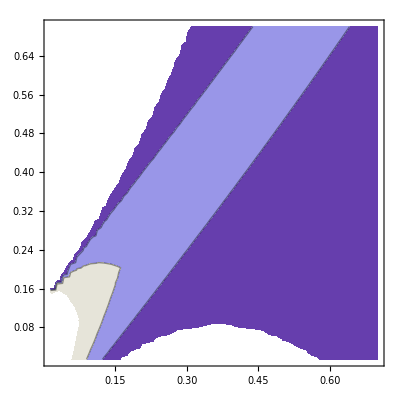

```mathematica
ListContourPlot[bb,Contours->{0,100,200,500},PlotRange->{0,Automatic}]
```

```mathematica
aa=Table[{results[[ind,5]],results[[ind,1]]*10^-9,If[Max[#]>242.2,Max[#],Min[#]]&[(Sign[#^2]Abs[#])&[results[[ind,3,3,{2,8}]]*10^-9]]},{ind,1,2500}];
```

```mathematica
ListPlot3D[bb,PlotRange->{0,500},MeshFunctions->{#3&},Mesh->4]
```

-Graphics3D-

```mathematica
ListPlot[{Table[{results[[ind,1]]/10^9,results[[ind,3,3,1]]/10^9},{ind,1,max}],Table[{results[[ind,1]]/10^9,results[[ind,3,3,2]]/10^9},{ind,1,max}],Table[{results[[ind,1]]/10^9,results[[ind,3,3,3]]/10^9},{ind,1,max}],Table[{results[[ind,1]]/10^9,results[[ind,3,3,4]]/10^9},{ind,1,max}],Table[{results[[ind,1]]/10^9,results[[ind,3,3,5]]/10^9},{ind,1,max}],Table[{results[[ind,1]]/10^9,results[[ind,3,3,6]]/10^9},{ind,1,max}],Table[{results[[ind,1]]/10^9,results[[ind,3,3,7]]/10^9},{ind,1,max}],Table[{results[[ind,1]]/10^9,results[[ind,3,3,8]]/10^9},{ind,1,max}]},
Joined->True,PlotRange->All,AxesOrigin->{0,0}]
```

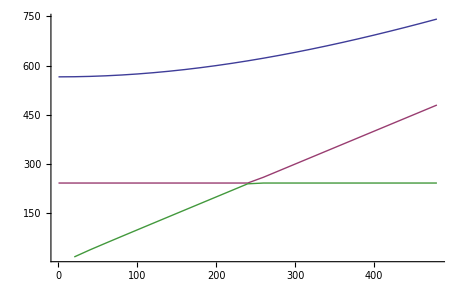

```mathematica
mNeutral/10^9*1.0
```

{640.403,299.806,242.113,242.113,242.113,242.113,242.113,242.113}

```mathematica
Save["/home/ruppell/Math/Hiller/dataMuTauViolationMFVscan-8-1k",{results}];
```

```mathematica
prec=50;
$MinPrecision=prec;
Abtm=SetPrecision[Aud,prec];  (*used with loops only*)
Akappa=SetPrecision[Aκ,prec];
Alambda=SetPrecision[Aλ,prec];
AlambdaN=SetPrecision[-250 GeV,prec];(* No effect? *)
An11=SetPrecision[TeV,prec];(* No effect? *)
An12=SetPrecision[TeV,prec];(* No effect? *)
An13=SetPrecision[TeV,prec];(* No effect? *)
Atau=SetPrecision[Ae,prec];
Atop=SetPrecision[Aud,prec]; (*used with loops only*)
kappa=SetPrecision[κ, prec];
ksi=SetPrecision[0,prec];(* Only neede for CPV *)
lambda=SetPrecision[λ, prec];
lambdaN=SetPrecision[0.07, prec];(* No effect? *)
M1=SetPrecision[Mone,prec];
M2=SetPrecision[2*Mone,prec];
MD33=MQ33=MU33=SetPrecision[Mqud,prec];(*used with loops only*)
ME11=ME22=ME33=ML11=ML22=ML33=SetPrecision[Mle,prec];
ME12=ME13=ME23=SetPrecision[0,prec];
ML12=ML13=ML23=SetPrecision[0,prec];
MN33=SetPrecision[100GeV,prec];
Rsc=SetPrecision[500GeV,prec]; (*used with loops only*)
vevS=SetPrecision[μ/lambda,prec];(* No effect? *)
Yn11=SetPrecision[10^-6,prec];
Yn12=SetPrecision[10^-6,prec];
Yn13=SetPrecision[10^-6,prec];
{valNsc,vecNsc}=Eigensystem[LN6];
{valCsc,vecCsc} = Eigensystem[LC3];
valN=Sqrt[Eigenvalues[Mnχ.Transpose[Conjugate[Mnχ]]]];
vecN=Inverse[Transpose[Eigenvectors[Mnχ.Transpose[Conjugate[Mnχ]]]]];
valC=Sqrt[Eigenvalues[Conjugate[McχCT].Mcχ]];
vecCU=Conjugate[Inverse[Transpose[Eigenvectors[Mcχ.Conjugate[McχCT]]]]];
vecCV=Inverse[Transpose[Eigenvectors[Conjugate[McχCT].Mcχ]]];
{valNsl,vecNsl}=Eigensystem[Chop[MslN]];
{valCsl,vecCsl}=Eigensystem[Chop[MslC]];
mHiggsN=Chop[Sqrt[valNsc]];vHiggsN=Chop[vecNsc];
mHiggsC=Chop[Sqrt[valCsc]];vHiggsC=Chop[vecCsc];
mNeutral=Chop[Sqrt[valNsl]];vNeutral=Chop[Inverse[Transpose[vecNsl]]];
mCharged=Chop[Sqrt[valCsl]];vCharged=Chop[Inverse[Transpose[vecCsl]]];
mCharginos=Chop[valC];{vecCU,vecCV}=Chop[{vecCU,vecCV}];
mNeutralinos=Chop[valN];vecN=Chop[vecN];
$MinPrecision=0;
MASS=N[{mHiggsN,mHiggsC,mNeutral,mCharged,mNeutralinos,mCharginos},4];
MIX=N[{vecNsc,vecCsc,vecNsl,vecCsl,vecN,vecCU,vecCV},4];
PAR=N[{{Tan[β],M1,M2,vevS},
{Abtm,Atop,Atau,Akappa,Alambda,AlambdaN,An11,An12,An13},
{kappa,ksi,lambda,lambdaN,Yn11,Yn12,Yn13},
{MD33,MQ33,MU33},
{ME11,ME22,ME33,ME12,ME13,ME23},
{ML11,ML22,ML33,ML12,ML13,ML23},
MN33,Rsc},4];
```

```mathematica
mNeutral*10^-9
```

{496.104,496.104,496.104,496.104,496.104,496.104,393.765,147.477}